```mathematica
Clear["Global`*"]
$Assumptions=True;
```

Dim initial value problem (ivp) (using halflife as scaling quantity):

```mathematica
mdl={deqn=c'[t]==-Log[2]c[t], iv=c[0]==1};
```

```mathematica
$Assumptions=c[t]>0&&t>0;
```

Solution:

Find the scale factors and replace them into the model:

```mathematica
sln=DSolve[mdl,c[t],t]
```

{{c[t]→2^-t}}

Get the solution and assign it to c:

```mathematica
c[t_]=c[t]/.sln[[1]]//FullSimplify
```

2^-t

Verify that the solution satisfies the ivp:

```mathematica
deqn//FullSimplify
```

True

```mathematica
iv//FullSimplify
```

True

Find limits:

```mathematica
Limit[c[t],t->0]
```

1

```mathematica
Limit[c[t],t->Infinity]
```

0

Find the value for which c is nul:

```mathematica
Solve[c[t]==0,t]
```

{}

Find the max and min:

```mathematica
FindMaximum[c[t],t]
```

General::ovfl: Overflow occurred in computation.

FindMaximum::nrnum: The function value Overflow[] is not a real number at {t} = {-7.595×10^15}.

{1.2491190956917871171535909144259768654845167607`15.954589770191005*^207847437739928,{t→-6.90454×10^14}}

```mathematica
FindMinimum[c[t],t]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{5.82623×10^-31,{t→100.437}}

Plot the solution:

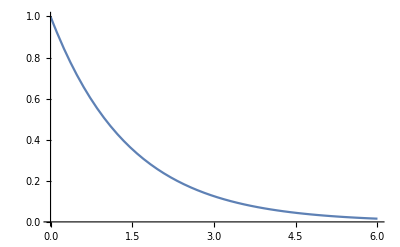

```mathematica
Plot[c[t],{t,0,6},PlotRange->{0,1}]
```